From the file ‘RefCurve_130143.txt.csv’.

```mathematica
t=Import["C:\\Users\\HILL\\Documents\\GitHub\\thesis\\figures\\oscillator\\guiding.csv"][[All,1]];
ch1=Import["C:\\Users\\HILL\\Documents\\GitHub\\thesis\\figures\\oscillator\\guiding.csv"][[All,2]];
ch2=Import["C:\\Users\\HILL\\Documents\\GitHub\\thesis\\figures\\oscillator\\guiding.csv"][[All,3]];
```

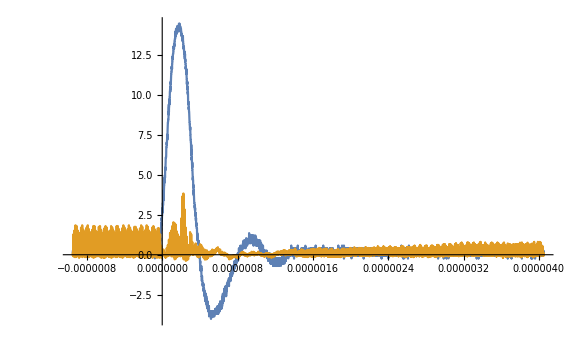

```mathematica
ListLinePlot[
{Thread[{t,ch1}],
Thread[{t,ch2*6}]},PlotRange->All,ImageSize->Large]
```